Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №2
 Задача Штурма-Лиувилля
Вариант №2

Выполнил: студент группы 0В01
Белясов Архип
Проверил: Богданов О.В.

Задание 1	
	Вычислить собственные значения и функции задачи Штурма - Лиувилля. Построить таблицу содержащую первые 5 собственных чисел и 5 собственных функций, изобразить их графически . Проверить ортогональность любой пары собственных функций . Сделать выводы.
-Graphics-

Случай 1

```mathematica
γ1=0;
α1 = {-1,0};
β1 = {1,0};
```

Случай 2

```mathematica
γ2= 0;
α2 = {1,0};
β2 = {-1,1};
```

Решение для случая 1

```mathematica
eqns={-y''[x]+γ1*y[x]==λ*y[x], α1[[1]]*y[0]+α1[[2]]*y'[0]==0,β1[[1]]*y[1]+β1[[2]]*y'[1]==0};
```

```mathematica
sol=DSolveValue[eqns,y[x],x]
```

Piecewise[{{C[1] Sin[x √λ], n∈ℤ&&((0==2 n π-2 √(n^2) π&&λ==4 n^2 π^2)||(0==π+2 n π-√((π+2 n π)^2)&&λ==(π+2 n π)^2))}, {0, True}}]

```mathematica
eifgfuns1=Table[sol//.{n->i,λ->(π+2n*π)^2}/.{C[1] ->1},{i,0,2}];
```

```mathematica
eifgfuns2=Table[sol//.{n->i,λ->(4 n^2 π^2)}/.{C[1] ->1},{i,0,3}];
```

Построим таблицу, содержащую 5-ть собственных значений и собственных функций

```mathematica
ownfun=Drop[Drop[Sort[Join[eifgfuns1,eifgfuns2]],-1],1]
```

{Sin[π x],Sin[2 π x],Sin[3 π x],Sin[4 π x],Sin[5 π x]}

```mathematica
ownlist={};
```

```mathematica
For[i=0,i<=3,i++,
AppendTo[ownlist,(4 *i^2 *π^2)];
AppendTo[ownlist,(π+2*i*π)^2];
]
```

```mathematica
ownlist=Drop[Drop[ownlist,1],{-2,-1}]
```

{π^2,4 π^2,9 π^2,16 π^2,25 π^2}

```mathematica
dataList=Join[{ownlist}, {ownfun}];
```

```mathematica
Grid[Join[{{"λ", "Собственные функции"}},Transpose[dataList]],Frame->All]
```

λ | Собственные функции
π^2 | Sin[π x]
4 π^2 | Sin[2 π x]
9 π^2 | Sin[3 π x]
16 π^2 | Sin[4 π x]
25 π^2 | Sin[5 π x]

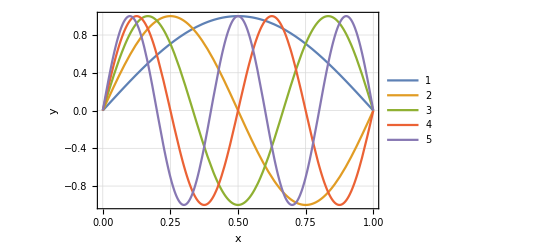

```mathematica
Plot[Evaluate[ownfun],{x,0,1},Frame->True,FrameLabel->{"x","y"},PlotLegends->Automatic,GridLines->Automatic]
```

Проверим ортогональность функций Sin[ π x] и Sin[2 π x]

```mathematica
Integrate[ownfun[[1]]*ownfun[[2]],{x,0,1}]
```

0

Случай 2

```mathematica
eqns={-y''[x]+γ2*y[x]==λ*y[x], α2[[1]]*y[0]+α2[[2]]*y'[0]==0,β2[[1]]*y[1]+β2[[2]]*y'[1]==0};
```

```mathematica
sol=DSolveValue[eqns,y[x],x]
```

Piecewise[{{C[1] Sin[x √λ], √λ Cos[√λ]==Sin[√λ]}, {0, True}}]

Найдем корни трансцендентного уравнения на собственные значения в диапазоне 10<λ<300

```mathematica
roots =λ /.Solve[√λ*Cos[√λ]==Sin[√λ]&&10<λ<300,λ];
```

```mathematica
data=Table[{λ,0},{λ,roots}];
```

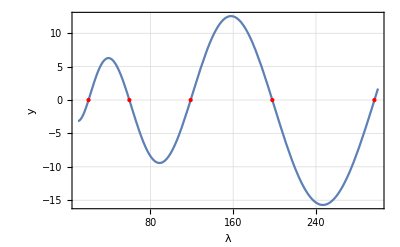

```mathematica
Plot[√λ*Cos[√λ]==Sin[√λ],{λ,10,300},Epilog->{PointSize[Large],Red,Point[data]},Frame->True,PlotLegends->Automatic,GridLines->Automatic,FrameLabel->{"λ","y"}]
```

```mathematica
eifgfuns3=Table[N[First[sol[[1,1]]]//.{C[1] ->1,λ->roots[[i]]}],{i,5}];
```

Построим таблицу, содержащую 5-ть собственных значений и собственных функций

```mathematica
list = {};
For[i=1,i<=5,i++,AppendTo[list,{N[roots[[i]]],N[First[sol[[1,1]]]//.{C[1] ->1,λ->roots[[i]]}]}]]
Grid[Join[{{"λ", "Собственные функции"}},list],Frame->All]
```

λ | Собственные функции
20.1907 | Sin[4.49341 x]
59.6795 | Sin[7.72525 x]
118.9 | Sin[10.9041 x]
197.858 | Sin[14.0662 x]
296.554 | Sin[17.2208 x]

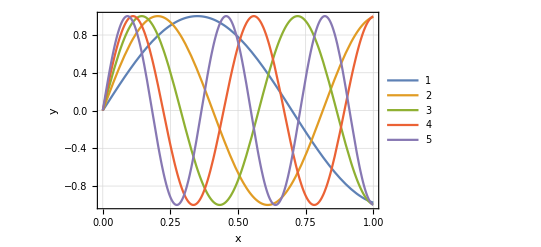

```mathematica
Plot[Evaluate[eifgfuns3],{x,0,1},Frame->True,FrameLabel->{"x","y"},PlotLegends->Automatic,GridLines->Automatic]
```

Проверим ортогональность функций Sin[4.49341 x] и Sin[7.72525 x]

```mathematica
Integrate[eifgfuns3[[1]]*eifgfuns3[[2]],{x,0,1}]
```

3.98986×10^-17

Вывод
	В результате выполнения первого задания было решено две задачи Штурма-Лиувилля, одна с граничными условиям первого рода слева и справа, а другая с граничными условиями первого рода слева  и с граничными условиями третьего рода справа. При решение первой задачи Штурма-Лиувилля получилось классическое условие на λ, из которого было найдено пять собственных значений. При решении второй задачи Штурма-Лиувилля получилось трансцендентного уравнение на собственные значения, решив которое было также получено пять λ. Кроме этого для каждой задачи был построен график, на котором изображено поведение пяти первых собственных функций. Также была проверена ортогональность любых двух собственных функций.

Задание 2
	Изучите пример на странице 9. Придумайте «работающий» в Wolfram 
Mathematica пример задачи Штурма-Лиувилля приводящий к спец. функциям

```mathematica
eqns={(1-x^2)*y''[x]-2x*y'[x]+λ*y[x]==0};
```

```mathematica
sol=DSolveValue[eqns,y[x],x,Assumptions->-1<x<1&&Abs[y[-1]]<Infinity&&Abs[y[+1]]<Infinity]
```

C[1] LegendreP[λ,x]+C[2] LegendreQ[λ,x]

```mathematica
eifgfuns4=Table[sol//.{λ->i*(i+1)}/.{C[1] ->1,C[2]->1},{i,0,4}];
```

```mathematica
dataList=Table[{i*(i+1),eifgfuns4[[i+1]]},{i,0,4}];
```

```mathematica
Grid[Join[{{"λ", "Собственные функции"}},dataList],Frame->All]
```

λ | Собственные функции
0 | 1-1/2 Log[1-x]+1/2 Log[1+x]
2 | -(3 x)/2+1/2 (-1+3 x^2)+1/2 (-1+3 x^2) (-1/2 Log[1-x]+1/2 Log[1+x])
6 | -(231 x)/80+(119 x^3)/8-(231 x^5)/16+1/16 (-5+105 x^2-315 x^4+231 x^6)+1/16 (-5+105 x^2-315 x^4+231 x^6) (-1/2 Log[1-x]+1/2 Log[1+x])
12 | (995215 x)/236544-(887107 x^3)/9216+(1548989 x^5)/2560-(3917667 x^7)/2560+(5143775 x^9)/3072-(676039 x^11)/1024+(231-18018 x^2+225225 x^4-1021020 x^6+2078505 x^8-1939938 x^10+676039 x^12)/1024+((231-18018 x^2+225225 x^4-1021020 x^6+2078505 x^8-1939938 x^10+676039 x^12) (-1/2 Log[1-x]+1/2 Log[1+x]))/1024
20 | (66586053015 x)/12108169216-(20766263345 x^3)/57933824+(5794847907 x^5)/851968-(26743310835 x^7)/458752+(105848501135 x^9)/393216-(95261730395 x^11)/131072+(77414998155 x^13)/65536-(74513229329 x^15)/65536+(156402792315 x^17)/262144-(34461632205 x^19)/262144+1/262144(46189-9699690 x^2+334639305 x^4-4461857400 x^6+30117537450 x^8-116454478140 x^10+273491577450 x^12-396713057400 x^14+347123925225 x^16-167890003050 x^18+34461632205 x^20)+1/262144(46189-9699690 x^2+334639305 x^4-4461857400 x^6+30117537450 x^8-116454478140 x^10+273491577450 x^12-396713057400 x^14+347123925225 x^16-167890003050 x^18+34461632205 x^20) (-1/2 Log[1-x]+1/2 Log[1+x])

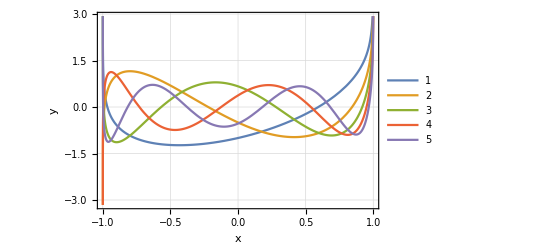

```mathematica
Plot[Evaluate[eifgfuns5],{x,-1,1},Frame->True,FrameLabel->{"x","y"},PlotLegends->Automatic,GridLines->Automatic]
```

Проверим ортогональность первых двух функций

```mathematica
Integrate[eifgfuns5[[1]]*eifgfuns5[[2]],{x,-1,1}]
```

0

Вывод
	В результате выполнения задания был придуман пример, приводящий к полиномам Лежандра.  Для данного примера было найдено пять собственных значений из условия λ_n=n(n+1) и пять собственных функций. Построена таблица для найденных λ и собственных функций. Кроме этого построен график, на котором изображено поведение пяти первых собственных функций. Также была проверена ортогональность любых двух собственных функций.